## Atomic Parameters

### Quantities will be normalized vs hydrogen

```mathematica
hydrogenAtomicRadius=N[QuantityMagnitude[ElementData[1,"AtomicRadius"]]]
```

53.

```mathematica
hydrogenAtomicCrossSection=π*hydrogenAtomicRadius^2
```

8824.73

```mathematica
hydrogenAtomicVolume=(4π)/3*hydrogenAtomicRadius^3
```

623615.

### Grabbing all other quantities

```mathematica
atomicRadii={#,N[QuantityMagnitude[ElementData[#,"AtomicRadius"]]]}&/@{26,14,6,13,5,15,31,32,29,47,79,30,22,23,24,40,41,42,72,73,74,58,59,64,92}(* In picometers *)
```

{{26,156.},{14,111.},{6,67.},{13,118.},{5,87.},{15,98.},{31,136.},{32,125.},{29,145.},{47,165.},{79,174.},{30,142.},{22,176.},{23,171.},{24,166.},{40,206.},{41,198.},{42,190.},{72,208.},{73,200.},{74,193.},{58,QuantityMagnitude[Missing[NotAvailable]]},{59,247.},{64,233.},{92,QuantityMagnitude[Missing[NotAvailable]]}}

```mathematica
atomicRadii⟦22,2⟧=248.
```

248.

```mathematica
atomicRadii⟦25,2⟧=230.
```

230.

```mathematica
atomicCrossSection = {#⟦1⟧,(π*(#⟦2⟧)^2)/hydrogenAtomicCrossSection}&/@atomicRadii (* In picometers squared *)
```

{{26,8.66358},{14,4.38626},{6,1.59808},{13,4.95692},{5,2.69455},{15,3.41901},{31,6.58455},{32,5.56248},{29,7.48487},{47,9.69206},{79,10.7782},{30,7.17836},{22,11.0274},{23,10.4098},{24,9.8099},{40,15.1072},{41,13.9566},{42,12.8515},{72,15.4019},{73,14.2399},{74,13.2606},{58,21.8953},{59,21.7191},{64,19.3268},{92,18.8323}}

```mathematica
atomicVolumes={#⟦1⟧,((4π)/3*(#⟦2⟧)^3)/hydrogenAtomicVolume}&/@atomicRadii (* In picometers cubed *)
```

{{26,25.5004},{14,9.18631},{6,2.02021},{13,11.0362},{5,4.42313},{15,6.32194},{31,16.8962},{32,13.1191},{29,20.4775},{47,30.1734},{79,35.3851},{30,19.2326},{22,36.6193},{23,33.5862},{24,30.7253},{40,58.7184},{41,52.1396},{42,46.0716},{72,60.4453},{73,53.7356},{74,48.2886},{58,102.454},{59,101.219},{64,84.965},{92,81.7252}}

```mathematica
atomicMasses={#,QuantityMagnitude[ElementData[#,"AtomicMass"]]}&/@{26,14,6,13,5,15,31,32,29,47,79,30,22,23,24,40,41,42,72,73,74,58,59,64,92}(* In amu *)
```

{{26,55.845},{14,28.085},{6,12.011},{13,26.9815385},{5,10.81},{15,30.973761998},{31,69.723},{32,72.63},{29,63.546},{47,107.8682},{79,196.966569},{30,65.38},{22,47.867},{23,50.9415},{24,51.9961},{40,91.224},{41,92.90637},{42,95.95},{72,178.49},{73,180.94788},{74,183.84},{58,140.116},{59,140.90766},{64,157.25},{92,238.02891}}

```mathematica
atomicValenceElectrons ={#,Total[Take[Flatten[ElementData[#,"ElectronConfiguration"]],-2]]}&/@{26,14,6,13,5,15,31,32,29,47,79,30,22,23,24,40,41,42,72,73,74,58,59,64,92}(* Doesn't work for Cu, Ag, Au, Zn, but is okay with early transitions *)
```

{{26,8},{14,4},{6,4},{13,3},{5,3},{15,5},{31,3},{32,4},{29,11},{47,11},{79,11},{30,12},{22,4},{23,5},{24,6},{40,4},{41,5},{42,6},{72,4},{73,5},{74,6},{58,3},{59,8},{64,3},{92,3}}

## Data Processing

### Import Database

```mathematica
rawData=Import["C:\\Users\\laris\\Documents\\MIT\\2018\\Summer\\Texas Research\\Final Data\\Database Curation\\CuratedDatabase7-26.csv"]
```

{1}
 |  |  |  |

```mathematica
rawLabels=rawData⟦1,1;;33⟧
```

{Fe,Si,C,Al,B,P,Ga,Ge,Cu,Ag,Au,Zn,Ti,V,Cr,Zr,Nb,Mo,Hf,Ta,W,Ce,Pr,Gd,U,Annealing temperature (K),Annealing Time (s),Primary Crystallization Onset (K),Primary Crystallization Peak (K),Secondary Crystallization Peak (K),Longitudinal Annealing field,Transverse Annealing field,Ribbon Thickness (um)}

### Splitting Database into Columns

```mathematica
featureColumns=rawData⟦2;;-1,#⟧&/@Range[1,Length[rawData⟦1⟧]]
```

{1}
 |  |  |  |

### Raw Features

```mathematica
percentFe = featureColumns⟦1⟧;
percentSi=featureColumns⟦2⟧;
percentC=featureColumns⟦3⟧;
percentAl=featureColumns⟦4⟧;
percentB=featureColumns⟦5⟧;
percentP=featureColumns⟦6⟧;
percentGa=featureColumns⟦7⟧;
percentGe=featureColumns⟦8⟧;
percentCu=featureColumns⟦9⟧;
percentAg=featureColumns⟦10⟧;
percentAu=featureColumns⟦11⟧;
percentZn=featureColumns⟦12⟧;
percentTi=featureColumns⟦13⟧;
percentV=featureColumns⟦14⟧;
percentCr=featureColumns⟦15⟧;
percentZr=featureColumns⟦16⟧;
percentNb=featureColumns⟦17⟧;
percentMo=featureColumns⟦18⟧;
percentHf=featureColumns⟦19⟧;
percentTa=featureColumns⟦20⟧;
percentW=featureColumns⟦21⟧;
percentCe=featureColumns⟦22⟧;
percentPr=featureColumns⟦23⟧;
percentGd=featureColumns⟦24⟧;
percentU=featureColumns⟦25⟧;
annealingTemp=featureColumns⟦26⟧;
annealingTime=featureColumns⟦27⟧;
primaryCrystalOnset=featureColumns⟦28⟧;
primaryCrystalPeak=featureColumns⟦29⟧;
secondaryCrystalPeak=featureColumns⟦30⟧;
laField=featureColumns⟦31⟧;
taField=featureColumns⟦32⟧;
ribbonThickness=featureColumns⟦33⟧;
```

```mathematica
rawFeatures = featureColumns⟦1;;33⟧;
```

```mathematica
earlyFeatures={percentTi,percentV,percentCr,percentZr,percentNb,percentMo,percentHf,percentTa,percentW,percentCe,percentPr,percentGd,percentU};
lateFeatures={percentCu,percentAg,percentAu,percentZn};
```

### Values

```mathematica
coercivity=featureColumns⟦34⟧;
curieTemp=featureColumns⟦35⟧;
coreLoss=featureColumns⟦36⟧;
electricalResistivity=featureColumns⟦37⟧;
permeability=featureColumns⟦38⟧;
magnetostriction=featureColumns⟦39⟧;
magneticSaturation=featureColumns⟦40⟧;
grainDiameter=featureColumns⟦41⟧;
doi = featureColumns⟦42⟧;
```

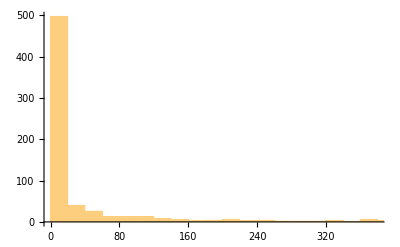

```mathematica
Histogram[coercivity]
```

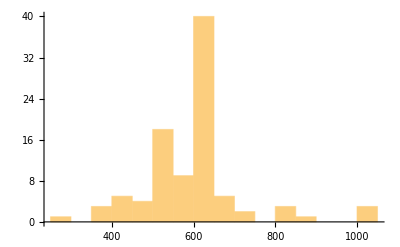

```mathematica
Histogram[curieTemp]
```

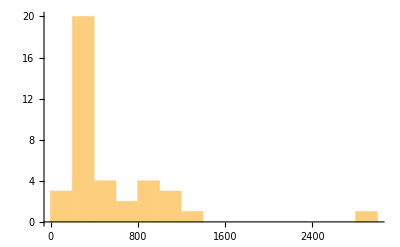

```mathematica
Histogram[coreLoss]
```

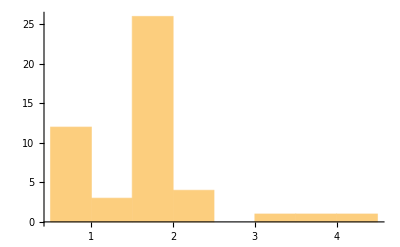

```mathematica
Histogram[electricalResistivity]
```

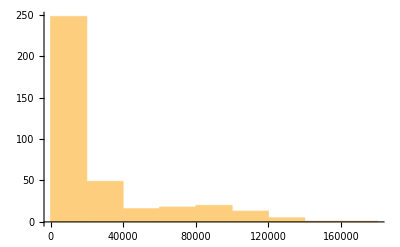

```mathematica
Histogram[permeability]
```

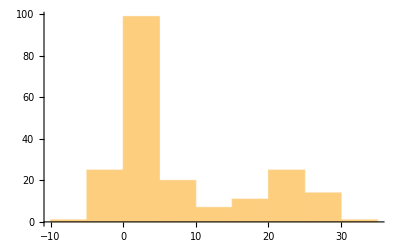

```mathematica
Histogram[magnetostriction]
```

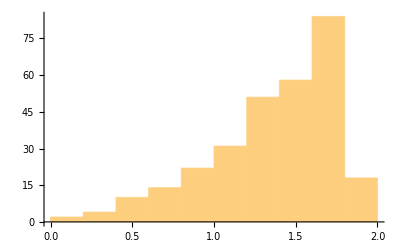

```mathematica
Histogram[magneticSaturation]
```

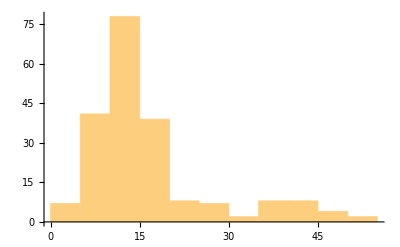

```mathematica
Histogram[grainDiameter]
```

### Simple Sum Transforms

```mathematica
percentSiCAl = Total[{percentSi,percentAl,percentC},{1}];(* Percent Si and Al and C combined *) 
percentBP=Total[{percentB,percentP},{1}] ;(* Percent B and P combined *) 
percentGaGe=Total[{percentGa,percentGe},{1}];(* Percent Ga and Ge combined *)
```

```mathematica
lateTransitionTotal =Total[lateFeatures,{1}];
```

```mathematica
earlyTransitionTotal = Total[earlyFeatures,{1}];
```

### Simple Multiplication/Division Transforms

```mathematica
relativeToFeSiCAl=N[percentSiCAl⟦#⟧/percentFe⟦#⟧]&/@Range[1,Length[percentFe]];
relativeToFeBP=N[percentBP⟦#⟧/percentFe⟦#⟧]&/@Range[1,Length[percentFe]];
relativeToFeGaGe=N[percentGaGe⟦#⟧/percentFe⟦#⟧]&/@Range[1,Length[percentFe]];
relativeToFeEarlyTransition =N[earlyTransitionTotal⟦#⟧/percentFe⟦#⟧]&/@Range[1,Length[percentFe]];
relativeToFeLateTransition=N[lateTransitionTotal⟦#⟧/percentFe⟦#⟧]&/@Range[1,Length[percentFe]];
```

```mathematica
relativeToLateEarly=Quiet[N[earlyTransitionTotal⟦#⟧/lateTransitionTotal⟦#⟧]&/@Range[1,Length[lateTransitionTotal]]]/.{Indeterminate->"",ComplexInfinity->""};
```

```mathematica
relativeToEarlySiCAl=Quiet[N[percentSiCAl⟦#⟧/earlyTransitionTotal⟦#⟧]&/@Range[1,Length[earlyTransitionTotal]]]/.{Indeterminate->"",ComplexInfinity->""};
relativeToLateSiCAl=Quiet[N[percentSiCAl⟦#⟧/lateTransitionTotal⟦#⟧]&/@Range[1,Length[lateTransitionTotal]]]/.{Indeterminate->"",ComplexInfinity->""};
```

```mathematica
relativeToEarlyBP=Quiet[N[percentBP⟦#⟧/earlyTransitionTotal⟦#⟧]&/@Range[1,Length[earlyTransitionTotal]]]/.{Indeterminate->"",ComplexInfinity->""};
relativeToLateBP=Quiet[N[percentBP⟦#⟧/lateTransitionTotal⟦#⟧]&/@Range[1,Length[lateTransitionTotal]]]/.{Indeterminate->"",ComplexInfinity->""};
```

```mathematica
relativeToEarlyGaGe=Quiet[N[percentGaGe⟦#⟧/earlyTransitionTotal⟦#⟧]&/@Range[1,Length[earlyTransitionTotal]]]/.{Indeterminate->"",ComplexInfinity->""};
relativeToLateGaGe=Quiet[N[percentGaGe⟦#⟧/lateTransitionTotal⟦#⟧]&/@Range[1,Length[lateTransitionTotal]]]/.{Indeterminate->"",ComplexInfinity->""};
```

### Weighted Average Transforms

#### Volume List

```mathematica
{volume[fe],
volume[si],
volume[c],
volume[al],
volume[b],
volume[p],
volume[ga],
volume[ge],
volume[cu],
volume[ag],
volume[au],
volume[zn],
volume[ti],
volume[v],
volume[cr],
volume[zr],
volume[nb],
volume[mo],
volume[hf],
volume[ta],
volume[w],
volume[ce],
volume[pr],
volume[gd],
volume[u]} = atomicVolumes⟦Flatten[Position[atomicVolumes,{#,_}]]⟧⟦1,2⟧ &/@ {26,14,6,13,5,15,31,32,29,47,79,30,22,23,24,40,41,42,72,73,74,58,59,64,92}
```

{25.5004,9.18631,2.02021,11.0362,4.42313,6.32194,16.8962,13.1191,20.4775,30.1734,35.3851,19.2326,36.6193,33.5862,30.7253,58.7184,52.1396,46.0716,60.4453,53.7356,48.2886,102.454,101.219,84.965,81.7252}

#### Cross Section List

```mathematica
{xArea[fe],
xArea[si],
xArea[c],
xArea[al],
xArea[b],
xArea[p],
xArea[ga],
xArea[ge],
xArea[cu],
xArea[ag],
xArea[au],
xArea[zn],
xArea[ti],
xArea[v],
xArea[cr],
xArea[zr],
xArea[nb],
xArea[mo],
xArea[hf],
xArea[ta],
xArea[w],
xArea[ce],
xArea[pr],
xArea[gd],
xArea[u]} = atomicCrossSection⟦Flatten[Position[atomicCrossSection,{#,_}]]⟧⟦1,2⟧ &/@ {26,14,6,13,5,15,31,32,29,47,79,30,22,23,24,40,41,42,72,73,74,58,59,64,92}
```

{8.66358,4.38626,1.59808,4.95692,2.69455,3.41901,6.58455,5.56248,7.48487,9.69206,10.7782,7.17836,11.0274,10.4098,9.8099,15.1072,13.9566,12.8515,15.4019,14.2399,13.2606,21.8953,21.7191,19.3268,18.8323}

#### Mass List

```mathematica
{mass[fe],
mass[si],
mass[c],
mass[al],
mass[b],
mass[p],
mass[ga],
mass[ge],
mass[cu],
mass[ag],
mass[au],
mass[zn],
mass[ti],
mass[v],
mass[cr],
mass[zr],
mass[nb],
mass[mo],
mass[hf],
mass[ta],
mass[w],
mass[ce],
mass[pr],
mass[gd],
mass[u]} = atomicMasses⟦Flatten[Position[atomicMasses,{#,_}]]⟧⟦1,2⟧ &/@ {26,14,6,13,5,15,31,32,29,47,79,30,22,23,24,40,41,42,72,73,74,58,59,64,92}
```

{55.845,28.085,12.011,26.9815385,10.81,30.973761998,69.723,72.63,63.546,107.8682,196.966569,65.38,47.867,50.9415,51.9961,91.224,92.90637,95.95,178.49,180.94788,183.84,140.116,140.90766,157.25,238.02891}

#### Valence Electron List

```mathematica
{vElectrons[fe],
vElectrons[si],
vElectrons[c],
vElectrons[al],
vElectrons[b],
vElectrons[p],
vElectrons[ga],
vElectrons[ge],
vElectrons[cu],
vElectrons[ag],
vElectrons[au],
vElectrons[zn],
vElectrons[ti],
vElectrons[v],
vElectrons[cr],
vElectrons[zr],
vElectrons[nb],
vElectrons[mo],
vElectrons[hf],
vElectrons[ta],
vElectrons[w],
vElectrons[ce],
vElectrons[pr],
vElectrons[gd],
vElectrons[u]} = atomicValenceElectrons⟦Flatten[Position[atomicValenceElectrons,{#,_}]]⟧⟦1,2⟧ &/@ {26,14,6,13,5,15,31,32,29,47,79,30,22,23,24,40,41,42,72,73,74,58,59,64,92}
```

{8,4,4,3,3,5,3,4,11,11,11,12,4,5,6,4,5,6,4,5,6,3,8,3,3}

#### Late Transition Transforms

```mathematica
{vElectrons[cu],vElectrons[ag],vElectrons[au],vElectrons[zn]}={2,1,3,2}
```

{2,1,3,2}

```mathematica
lateVolumes={volume[cu],volume[ag],volume[au],volume[zn]};
lateXAreas ={xArea[cu],xArea[ag],xArea[au],xArea[zn]};
lateMasses={mass[cu],mass[ag],mass[au],mass[zn]};
lateVElectrons={vElectrons[cu],vElectrons[ag],vElectrons[au],vElectrons[zn]};
```

```mathematica
lateTransitionWeightedVolume = Quiet[ Total[lateVolumes⟦#⟧*lateFeatures⟦#⟧&/@Range[1,Length[lateFeatures]],{1}]/lateTransitionTotal]/.{Indeterminate->0};
lateTransitionWeightedArea = Quiet[ Total[lateXAreas⟦#⟧*lateFeatures⟦#⟧&/@Range[1,Length[lateFeatures]],{1}]/lateTransitionTotal]/.{Indeterminate->0};
lateTransitionWeightedMass = Quiet[ Total[lateMasses⟦#⟧*lateFeatures⟦#⟧&/@Range[1,Length[lateFeatures]],{1}]/lateTransitionTotal]/.{Indeterminate->0};
lateTransitionMeanVElectrons = Quiet[Total[N@lateVElectrons⟦#⟧*lateFeatures⟦#⟧&/@Range[1,Length[lateFeatures]],{1}]/lateTransitionTotal]/.{Indeterminate->0};
```

#### Early Transition Transforms

```mathematica
earlyVolumes={volume[ti],volume[v],volume[cr],volume[zr],volume[nb],volume[mo],volume[hf],volume[ta],volume[w],volume[ce],volume[pr],volume[gd],volume[u]};
earlyXAreas ={xArea[ti],xArea[v],xArea[cr],xArea[zr],xArea[nb],xArea[mo],xArea[hf],xArea[ta],xArea[w],xArea[ce],xArea[pr],xArea[gd],xArea[u]};
earlyMasses={mass[ti],mass[v],mass[cr],mass[zr],mass[nb],mass[mo],mass[hf],mass[ta],mass[w],mass[ce],mass[pr],mass[gd],mass[u]};
earlyVElectrons={vElectrons[ti],vElectrons[v],vElectrons[cr],vElectrons[zr],vElectrons[nb],vElectrons[mo],vElectrons[hf],vElectrons[ta],vElectrons[w],vElectrons[ce],vElectrons[pr],vElectrons[gd],vElectrons[u]};
```

```mathematica
earlyTransitionWeightedVolume = Quiet[ Total[earlyVolumes⟦#⟧*earlyFeatures⟦#⟧&/@Range[1,Length[earlyFeatures]],{1}]/earlyTransitionTotal]/.{Indeterminate->0};
earlyTransitionWeightedArea = Quiet[ Total[earlyXAreas⟦#⟧*earlyFeatures⟦#⟧&/@Range[1,Length[earlyFeatures]],{1}]/earlyTransitionTotal]/.{Indeterminate->0};
earlyTransitionWeightedMass = Quiet[ Total[earlyMasses⟦#⟧*earlyFeatures⟦#⟧&/@Range[1,Length[earlyFeatures]],{1}]/earlyTransitionTotal]/.{Indeterminate->0};
earlyTransitionMeanVElectrons = Quiet[1/earlyTransitionTotal Total[N@earlyVElectrons⟦#⟧*earlyFeatures⟦#⟧&/@Range[1,Length[earlyFeatures]],{1}]]/.{Indeterminate->0};
```

### Temperature Differences

```mathematica
deltaT0=annealingTemp-primaryCrystalOnset/.___-_ -> "";
deltaT1=annealingTemp-primaryCrystalPeak/.___-_ -> "";
deltaT2=annealingTemp-secondaryCrystalPeak/.___-_ -> "";
```

### Element Identity String

```mathematica
elementFeatures = {percentFe, percentSi,percentC,percentAl,percentB,percentP,percentGa,percentGe,lateTransitionTotal,earlyTransitionTotal}
```

{1}
 |  |  |  |

```mathematica
compRows = Transpose[elementFeatures]
```

{{72.5,13.5,0,0,9,0,0,1,1,3},{71.5,9.5,0,1,9,0,0,5,1,3},{73.5,13.5,0,0,9,0,0,0,1,3},{73.5,13.5,0,0,9,0,0,0,1,3},{73.5,13.5,0,0,7,0,0,2,1,3},1284,{81,4,0,0,13,0,0,0,2,0},{81.3,4,0,0,13,0,0,0,1.7,0},{81.3,4,0,0,13,0,0,0,1.7,0},{81.3,4,0,0,13,0,0,0,1.7,0},{81,4,0,0,13,0,0,0,2,0}}
 |  |  |  |

```mathematica
isPresent[amount_]:= Piecewise[{{"0", amount==0}, {"1", amount≠ 0}}]
```

```mathematica
compID[elements_]:= Module[
{compstring=""},
For[
i=1,i≤Length[elements],i++,
compstring=compstring<>isPresent[elements⟦i⟧]
];
compstring
]
```

```mathematica
compIDColumn = compID[#]&/@ compRows;
```

## New Data Set

```mathematica
newLabels={"Total SiCAl","Total BP","Total GaGe","Total Late Transition","Total Early Transition","Relative to Fe SiCAl","Relative to Fe BP","Relative to Fe GaGe","Relative to Fe Early","Relative to Fe Late","Relative to Late Early","Relative to Early SiCAl","Relative to Late SiCAl","Relative to Early BP","Relative to Late BP","Relative to Early GaGe","Relative to Late GaGe","Late Weighted Volume","Late Weighted Area","Late Weighted Mass","Late Mean Electrons","Early Weighted Volume","Early Weighted Area","Early Weighted Mass","Early Mean Electrons","Delta T0","Delta T1","Delta T2"};
```

```mathematica
allLabels=Join[newLabels,rawLabels];
```

```mathematica
newFeatures={percentSiCAl,percentBP,percentGaGe,lateTransitionTotal,earlyTransitionTotal,relativeToFeSiCAl,relativeToFeBP,relativeToFeGaGe,relativeToFeEarlyTransition,relativeToFeLateTransition,relativeToLateEarly,relativeToEarlySiCAl,relativeToLateSiCAl,relativeToEarlyBP,relativeToLateBP,relativeToEarlyGaGe,relativeToLateGaGe,lateTransitionWeightedVolume,lateTransitionWeightedArea,lateTransitionWeightedMass,lateTransitionMeanVElectrons,earlyTransitionWeightedVolume,earlyTransitionWeightedArea,earlyTransitionWeightedMass,earlyTransitionMeanVElectrons,deltaT0,deltaT1,deltaT2};
```

```mathematica
allFeatures=Join[newFeatures,rawFeatures];
```

```mathematica
targets={{coercivity,"Coercivity"},{curieTemp,"Curie Temp"},{coreLoss,"Core Loss"},{electricalResistivity,"Electrical Resistivity"},{permeability,"Permeability"},{magnetostriction,"Magnetostriction"},{magneticSaturation,"Magnetic Saturation"},{grainDiameter,"Grain Diameter"},{compIDColumn,"Composition ID"},{doi,"Reference DOI"}};
```

```mathematica
masterDataset=Prepend[Transpose[Join[allFeatures,targets⟦All,1⟧]],Join[allLabels,targets⟦All,2⟧]]
Export["MasterDataset7-26.csv",masterDataset]
```

{{Total SiCAl,Total BP,Total GaGe,Total Late Transition,Total Early Transition,Relative to Fe SiCAl,Relative to Fe BP,Relative to Fe GaGe,55,Core Loss,Electrical Resistivity,Permeability,Magnetostriction,Magnetic Saturation,Grain Diameter,Composition ID,Reference DOI},1293,{1}}
 |  |  |  |

MasterDataset7-26.csv

```mathematica
(*fullFeatureDataSet[{target_,label_}]:= Prepend[Transpose[Join[allFeatures,{target}]],Join[allLabels,{label}]]
newFeatureDataSet[{target_,label_}]:= Prepend[Transpose[Join[newFeatures,{target}]],Join[newLabels,{label}]]
rawFeatureDataSet[{target_,label_}]:= Prepend[Transpose[Join[rawFeatures,{target}]],Join[rawLabels,{label}]]*)
```

```mathematica
(*fullFeatureDataSets=fullFeatureDataSet[#]&/@targets;
newFeatureDataSets=newFeatureDataSet[#]&/@targets;
rawFeatureDataSets=rawFeatureDataSet[#]&/@targets;*)
```

```mathematica
(*Export["FullFeatureCoercivity.csv",fullFeatureDataSets⟦1⟧]
Export["FullFeatureCurieTemp.csv",fullFeatureDataSets⟦2⟧]
Export["FullFeatureCoreLoss.csv",fullFeatureDataSets⟦3⟧]
Export["FullFeatureElectricalResistivity.csv",fullFeatureDataSets⟦4⟧]
Export["FullFeaturePermeability.csv",fullFeatureDataSets⟦5⟧]
Export["FullFeatureMagnetostriction.csv",fullFeatureDataSets⟦6⟧]
Export["FullFeatureMagneticSaturation.csv",fullFeatureDataSets⟦7⟧]
Export["FullFeatureGrainDiameter.csv",fullFeatureDataSets⟦8⟧]
Export["FullFeatureLatticeParameter.csv",fullFeatureDataSets⟦9⟧]*)
```

```mathematica
(*Export["NewFeatureCoercivity.csv",newFeatureDataSets⟦1⟧]
Export["NewFeatureCurieTemp.csv",newFeatureDataSets⟦2⟧]
Export["NewFeatureCoreLoss.csv",newFeatureDataSets⟦3⟧]
Export["NewFeatureElectricalResistivity.csv",newFeatureDataSets⟦4⟧]
Export["NewFeaturePermeability.csv",newFeatureDataSets⟦5⟧]
Export["NewFeatureMagnetostriction.csv",newFeatureDataSets⟦6⟧]
Export["NewFeatureMagneticSaturation.csv",newFeatureDataSets⟦7⟧]
Export["NewFeatureGrainDiameter.csv",newFeatureDataSets⟦8⟧]
Export["NewFeatureLatticeParameter.csv",newFeatureDataSets⟦9⟧]*)
```

```mathematica
(*Export["RawFeatureCoercivity.csv",rawFeatureDataSets⟦1⟧]
Export["RawFeatureCurieTemp.csv",rawFeatureDataSets⟦2⟧]
Export["RawFeatureCoreLoss.csv",rawFeatureDataSets⟦3⟧]
Export["RawFeatureElectricalResistivity.csv",rawFeatureDataSets⟦4⟧]
Export["RawFeaturePermeability.csv",rawFeatureDataSets⟦5⟧]
Export["RawFeatureMagnetostriction.csv",rawFeatureDataSets⟦6⟧]
Export["RawFeatureMagneticSaturation.csv",rawFeatureDataSets⟦7⟧]
Export["RawFeatureGrainDiameter.csv",rawFeatureDataSets⟦8⟧]
Export["RawFeatureLatticeParameter.csv",rawFeatureDataSets⟦9⟧]*)
```